# Demonstrating CoulombHiggs

Boris Pioline, June 10, 2014; based on work with Jan Manschot and Ashoke Sen; updated Dec 2020

Download CoulombHiggs.m from http://www.lpthe.jussieu.fr/~pioline/computing.html

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.0 - A package for evaluating quiver invariants

## Kronecker quiver

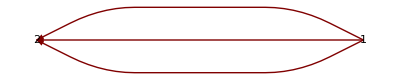

3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6

3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6

```mathematica
Mat={{0,3},{-3,0}};Nvec={3,2};Cvec={1,-1};
$QuiverVerbose=False;
QuiverPlot[Mat]
Simplify[CoulombBranchFormula[Mat,Cvec,Nvec]]
Simplify[HiggsBranchFormula[Mat,Cvec,Nvec]]
```

## Three-node quiver with loop

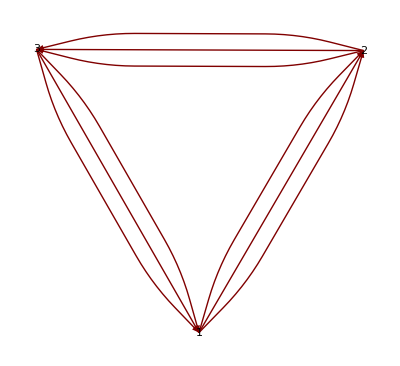

-1/y-y+OmS[{1,1,1},y,t]

```mathematica
aa=3;bb=3;cc=3;
Mat=({{0, aa, -cc}, {-aa, 0, bb}, {cc, -bb, 0}});
Nvec={1,1,1};Cvec={1,-3,2};
QuiverPlot[Mat]
Simplify[CoulombBranchFormula[Mat,Cvec,Nvec]]
```

## Cyclic quivers

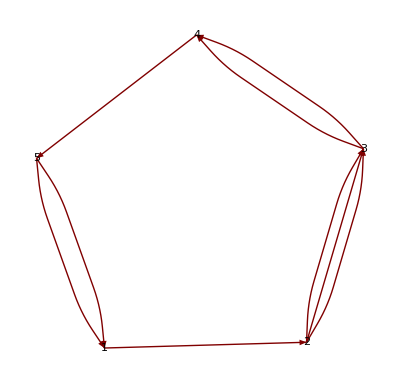

((1+y^2)^4-(y^3+y^5) OmS[{1,1,1,1,1},y,t]+y^4 OmS[{1,2,1,1,1},y,t])/y^4

```mathematica
Mat=CyclicQuiverDSZ[{1,3,2,1,2}];
Nvec={1,2,1,1,1};
Cvec=-AttractorFI[Mat,Nvec];
QuiverPlot[Mat]
Simplify[CoulombBranchFormula[Mat,Cvec,Nvec]]
```